# Parameters

```mathematica
dir="sample_traj";
dirLP="sample_traj_lp";
dirIxns="learn_centered";
optStepRead=980;
timepointMax=500;
allTheta={"hX","hY","wXX1","wYY1","bX1","bY1","wX1X2","wY1Y2","bX2","bY2"};
allBiases={"hX","hY","bX1","bY1","bX2","bY2"};
allWeights={"wXX1","wYY1","wX1X2","wY1Y2"};
boxLength=40;
dt=1.0;
figureDir="figures";
```

# Lattice

```mathematica
fMakePlots[timepoint_,iChain_,BP_]:=Module[{data1,dataX1,data11,dataY1,boxLength,plts,data111},
boxLength=40;
plts={{},{}};

SetDirectory[NotebookDirectory[]];
Do[
data1=Import["../data/"<>dirIxns<>"/"<>dirLP<>"/"<>IntegerString[timepoint,10,4]<>"/lattices/layer_"<>IntegerString[i,10,1]<>"_"<>IntegerString[iChain,10,4]<>".txt","Table"];
If[BP[[i+1]]=="binary",
data11=ConstantArray[0,{boxLength,boxLength}];
dataX1=Select[data1,StringTake[#[[3]],1]=="X"&][[;;,{1,2}]];
dataY1=Select[data1,StringTake[#[[3]],1]=="Y"&][[;;,{1,2}]];
Do[
data11[[pt[[1]],pt[[2]]]]=Black;
,{pt,dataX1}];
Do[
data11[[pt[[1]],pt[[2]]]]=Blue;
,{pt,dataY1}];

AppendTo[plts[[1]],ArrayPlot[data11,ImageSize->200]];
AppendTo[plts[[2]],Null];
,
data11=ConstantArray[0,{boxLength,boxLength}];
data111=ConstantArray[0,{boxLength,boxLength}];
Do[
data11[[pt[[1]],pt[[2]]]]=Opacity[pt[[4]],Black];
data111[[pt[[1]],pt[[2]]]]=Opacity[pt[[6]],Blue];
,{pt,data1}];

AppendTo[plts[[1]],ArrayPlot[data11,ImageSize->200]];
AppendTo[plts[[2]],ArrayPlot[data111,ImageSize->200]];
];
,{i,0,2}];

Return[
Grid[Reverse[Transpose[plts]]]]
];
```

```mathematica
Manipulate[fMakePlots[370,iLatt,{"prob","prob","prob"}],{iLatt,0,100-1,1}]
```

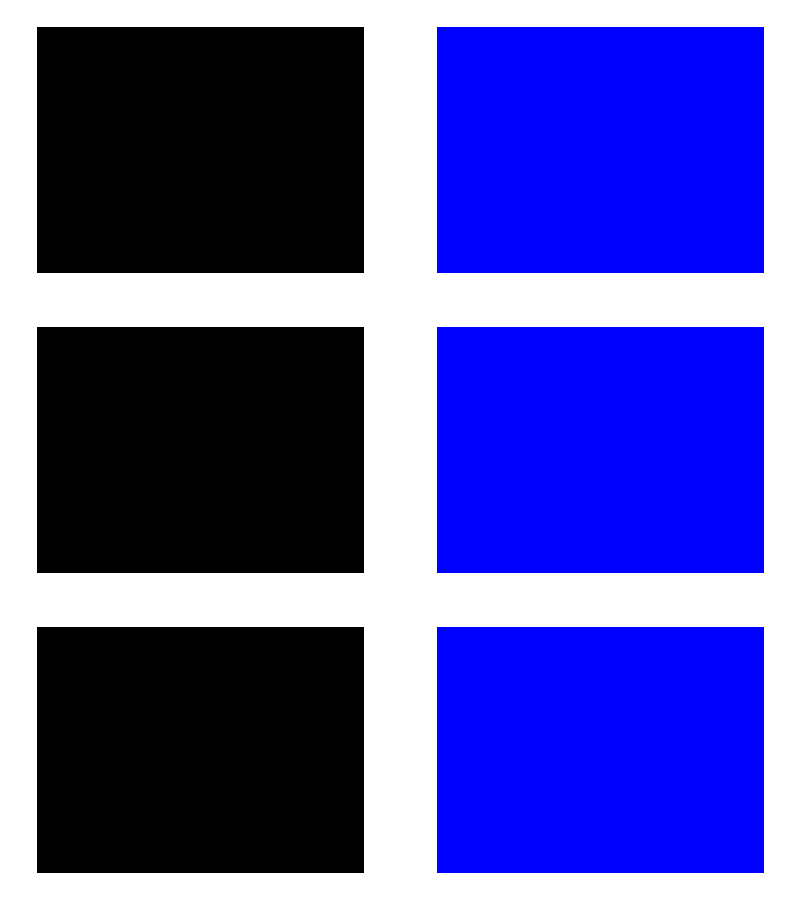

```mathematica
timepointChosen=370;
iLattChosen=53;
pltLattices=fMakePlots[timepointChosen,iLattChosen,{"prob","prob","prob"}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
If[!DirectoryQ[figureDir],CreateDirectory[figureDir]];
Export[figureDir<>"/lattices.pdf",pltLattices]
```

figures_dbm/lattices.pdf

# Ixn params

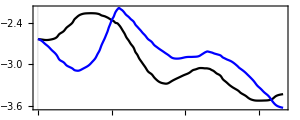
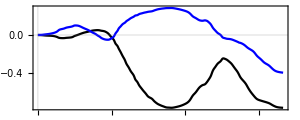
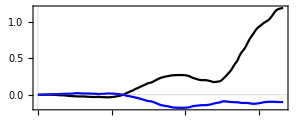
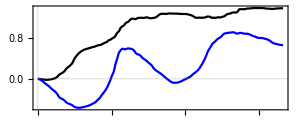
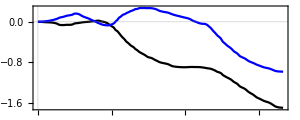

```mathematica
{pltIxna0,pltIxna1,pltIxna2,pltIxnw01,pltIxnw12}=Module[{dataParams},
SetDirectory[NotebookDirectory[]];
dataParams=Association[];
Do[
dataParams[ixn]=Import["../data/"<>dirIxns<>"/ixn_params/"<>ixn<>"_"<>IntegerString[optStepRead,10,5]<>".txt","Table"];
,{ixn,allTheta}];
{
ListLinePlot[{dataParams["hX"],dataParams["hY"]},PlotRange->All,ImageSize->300,PlotStyle->{Black,Blue},AspectRatio->0.4],
ListLinePlot[{dataParams["bX1"],dataParams["bY1"]},PlotRange->All,ImageSize->300,PlotStyle->{Black,Blue},AspectRatio->0.4],
ListLinePlot[{dataParams["bX2"],dataParams["bY2"]},PlotRange->All,ImageSize->300,PlotStyle->{Black,Blue},AspectRatio->0.4,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}}],
ListLinePlot[{dataParams["wXX1"],dataParams["wYY1"]},PlotRange->All,ImageSize->300,PlotStyle->{Black,Blue},AspectRatio->0.4],
ListLinePlot[{dataParams["wX1X2"],dataParams["wY1Y2"]},PlotRange->All,ImageSize->300,PlotStyle->{Black,Blue},AspectRatio->0.4]
}
]
```

```mathematica
leg=LineLegend[{Black,Blue},{"α → Prey","α → Hunter"},LabelStyle->Directive[FontSize->30],LegendMarkerSize->40]
```

```mathematica
SetDirectory[NotebookDirectory[]];
If[!DirectoryQ[figureDir],CreateDirectory[figureDir]];
Export[figureDir<>"/ixns_a0.pdf",pltIxna0];
Export[figureDir<>"/ixns_a1.pdf",pltIxna1];
Export[figureDir<>"/ixns_a2.pdf",pltIxna2];
Export[figureDir<>"/ixns_w01.pdf",pltIxnw01];
Export[figureDir<>"/ixns_w12.pdf",pltIxnw12];
```

```mathematica
SetDirectory[NotebookDirectory[]];
If[!DirectoryQ[figureDir],CreateDirectory[figureDir]];
Export[figureDir<>"/ixns_2.pdf",pltIxn2]
```

figures_dbm/ixns_2.pdf

```mathematica
SetDirectory[NotebookDirectory[]];
If[!DirectoryQ[figureDir],CreateDirectory[figureDir]];
Export[figureDir<>"/leg_ixns.pdf",leg]
```

figures_dbm/leg_ixns.pdf

# Moments: X = mean number of prey

## Plot

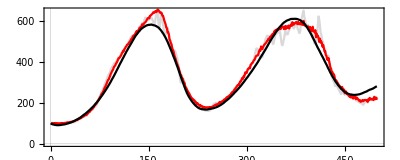

```mathematica
pltMomentX=
Module[{countsVraw,countsVLP,iLattStart,iLattEnd,countsX},
countsVraw=Association[];
Do[
countsVraw[timepoint]=Import["../data/"<>dirIxns<>"/"<>dir<>"/"<>IntegerString[timepoint,10,4]<>"/moments/moments.txt","Table"][[{1,2},2]];
,{timepoint,0,timepointMax-1}];
countsVraw=Values[countsVraw];

countsVLP=Association[];
Do[
countsVLP[timepoint]=Import["../data/"<>dirIxns<>"/"<>dirLP<>"/"<>IntegerString[timepoint,10,4]<>"/moments/moments.txt","Table"][[{1,2},2]];
,{timepoint,0,timepointMax-1}];
countsVLP=Values[countsVLP];

iLattStart=1;
iLattEnd=100;
countsX={};
Do[
AppendTo[countsX,Import["../../stoch_sims/data/lattice_v"<>IntegerString[iLatt,10,3]<>"/counts/X.txt","Table"]];
,{iLatt,iLattStart,iLattEnd}];
countsX=Mean[countsX]//N;

Show[ListLinePlot[Transpose[countsVraw][[1]],PlotStyle->{LightGray}],ListLinePlot[Transpose[countsVLP][[1]],PlotStyle->Red],ListLinePlot[countsX,PlotStyle->Black],AspectRatio->0.4]
]
```

```mathematica
legMomentX=LineLegend[{Black,LightGray,Red},{"Stoch. sim.","Learned","Learned (filtered)"},LabelStyle->Directive[FontSize->28],LegendMarkerSize->40]
```

```mathematica
SetDirectory[NotebookDirectory[]];
If[!DirectoryQ[figureDir],CreateDirectory[figureDir]];
Export[figureDir<>"/moment_X.pdf",pltMomentX]
```

figures_dbm/moment_X.pdf

```mathematica
SetDirectory[NotebookDirectory[]];
If[!DirectoryQ[figureDir],CreateDirectory[figureDir]];
Export[figureDir<>"/leg_moment.pdf",legMomentX]
```

figures_dbm/leg_moment.pdf

## Channels

```mathematica
{dataCovLP,derivs,channels}=Module[{dataParams,dataCov,tmp,channels,derivs,dataCovLP},

SetDirectory[NotebookDirectory[]];

(* Import params *)
dataParams=Association[];
Do[
dataParams[theta]=Import["../data/"<>dirIxns<>"/ixn_params_lp/"<>theta<>"_"<>IntegerString[optStepRead,10,5]<>".txt","Table"][[;;,2]];
,{theta,allTheta}];

(* Derivs *)
derivs=Association[];
Do[
derivs[theta]=(RotateLeft[dataParams[theta]][[;;-2]]-dataParams[theta][[;;-2]])/dt;
,{theta,allTheta}];

(* Import covs *)
dataCov=Association[];
Do[
dataCov[theta]={};
,{theta,allTheta}];
Do[
tmp=Import["../data/"<>dirIxns<>"/"<>dirLP<>"/"<>IntegerString[timepoint,10,4]<>"/covs/hX.txt","Table"];
Do[
AppendTo[dataCov[tmp[[i,1]]],tmp[[i,2]]];
,{i,1,Length[tmp]}];
,{timepoint,0,timepointMax-1}];
dataCovLP=Association[];
Do[
dataCovLP[theta]=LowpassFilter[dataCov[theta],0.1];
,{theta,allTheta}];

(* Multiply *)
channels=Association[];
Do[
channels[theta]={};
,{theta,allTheta}];

Do[
Do[
AppendTo[channels[theta],dataCovLP[theta][[timepoint+1]]*derivs[theta][[timepoint+1]]];
,{theta,allTheta}];

,{timepoint,0,timepointMax-2}];

{dataCovLP,derivs,channels}
];
```

```mathematica
cols1=Association[];
cols1["hX"]={Black};
cols1["hY"]={Blue};
cols1["bX1"]={Black,Dashed};
cols1["bY1"]={Blue,Dashed};
cols1["bX2"]={Black,DotDashed};
cols1["bY2"]={Blue,DotDashed};

cols2=Association[];
cols2["wXX1"]={Black};
cols2["wYY1"]={Blue};
cols2["wX1X2"]={Black,Dashed};
cols2["wY1Y2"]={Blue,Dashed};
```

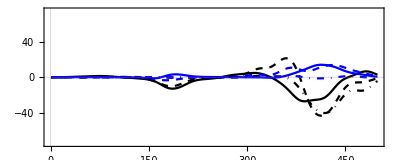

```mathematica
pltXchannelBias=ListLinePlot[Table[channels[theta],{theta,allBiases}],PlotRange->{-75,75},PlotStyle->Values[cols1],AspectRatio->0.4]
```

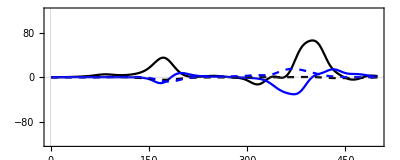

```mathematica
pltXchannelWeights=ListLinePlot[Table[channels[theta],{theta,allWeights}],PlotRange->{-120,120},PlotStyle->Values[cols2],AspectRatio->0.4]
```

```mathematica
SetDirectory[NotebookDirectory[]];
If[!DirectoryQ[figureDir],CreateDirectory[figureDir]];
Export[figureDir<>"/channels_X_bias.pdf",pltXchannelBias]
```

figures_dbm/channels_X_bias.pdf

```mathematica
SetDirectory[NotebookDirectory[]];
If[!DirectoryQ[figureDir],CreateDirectory[figureDir]];
Export[figureDir<>"/channels_X_weights.pdf",pltXchannelWeights]
```

figures_dbm/channels_X_weights.pdf

```mathematica
legBias2=LineLegend[Directive@@@Values[cols1][[4;;]],{"a_H^(1)","a_P^(2)","a_H^(2)"},LabelStyle->Directive[FontSize->28],LegendMarkerSize->40]
```

```mathematica
legBias1=LineLegend[Directive@@@Values[cols1][[;;3]],{"a_P^(0)","a_H^(0)","a_P^(1)"},LabelStyle->Directive[FontSize->28],LegendMarkerSize->40]
```

```mathematica
legWeights2=LineLegend[Directive@@@Values[cols2][[3;;]],{"W_PP^(1, 2)","W_HH^(1, 2)"},LabelStyle->Directive[FontSize->28],LegendMarkerSize->40]
```

```mathematica
legWeights1=LineLegend[Directive@@@Values[cols2][[;;2]],{"W_PP^(0, 1)","W_HH^(0, 1)"},LabelStyle->Directive[FontSize->28],LegendMarkerSize->40]
```

```mathematica
SetDirectory[NotebookDirectory[]];
If[!DirectoryQ[figureDir],CreateDirectory[figureDir]];
Export[figureDir<>"/leg_weight_1.pdf",legWeights1]
```

figures_dbm/leg_weight_1.pdf

```mathematica
SetDirectory[NotebookDirectory[]];
If[!DirectoryQ[figureDir],CreateDirectory[figureDir]];
Export[figureDir<>"/leg_weight_2.pdf",legWeights2]
```

figures_dbm/leg_weight_2.pdf

```mathematica
SetDirectory[NotebookDirectory[]];
If[!DirectoryQ[figureDir],CreateDirectory[figureDir]];
Export[figureDir<>"/leg_bias_1.pdf",legBias1]
```

figures_dbm/leg_bias_1.pdf

```mathematica
SetDirectory[NotebookDirectory[]];
If[!DirectoryQ[figureDir],CreateDirectory[figureDir]];
Export[figureDir<>"/leg_bias_2.pdf",legBias2]
```

figures_dbm/leg_bias_2.pdf

## True derivative

```mathematica
derivTrue={};
Do[
dataNext=Import["../data/"<>dirIxns<>"/"<>dirLP<>"/"<>IntegerString[timepoint+1,10,4]<>"/moments/moments.txt","Table"];
dataThis=Import["../data/"<>dirIxns<>"/"<>dirLP<>"/"<>IntegerString[timepoint,10,4]<>"/moments/moments.txt","Table"];
AppendTo[derivTrue,(dataNext[[1,2]]-dataThis[[1,2]])/dt];
,{timepoint,0,timepointMax-2}];
```

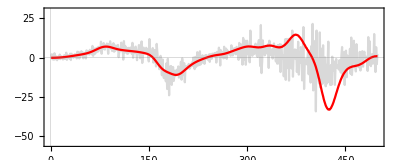

```mathematica
pltSumX=ListLinePlot[{derivTrue,Total[Values[channels]]},PlotStyle->{LightGray,Red},PlotRange->{-55,30},AspectRatio->0.4]
```

```mathematica
SetDirectory[NotebookDirectory[]];
If[!DirectoryQ[figureDir],CreateDirectory[figureDir]];
Export[figureDir<>"/sum_X.pdf",pltSumX]
```

figures_dbm/sum_X.pdf

```mathematica
legSum=LineLegend[{LightGray,Red},{"Stoch. sim.","Learned (filtered)"},LabelStyle->Directive[FontSize->28],LegendMarkerSize->40]
```

```mathematica
SetDirectory[NotebookDirectory[]];
If[!DirectoryQ[figureDir],CreateDirectory[figureDir]];
Export[figureDir<>"/leg_sum.pdf",legSum]
```

figures_dbm/leg_sum.pdf

# Moments: NNs XX

## Plot

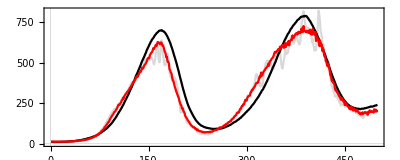

```mathematica
pltnnXX=Module[{moments,dat,momentsTrue,momentsLP,vs},
vs={"nn XX"};
moments=Association[];
Do[
moments[v]={};
,{v,vs}];
Do[
dat=Import["../data/"<>dirIxns<>"/"<>dir<>"/"<>IntegerString[timepoint,10,4]<>"/moments/moments_other.txt","Table"];
AppendTo[moments[vs[[1]]],dat[[1,3]]];
,{timepoint,0,timepointMax-1}];

momentsLP=Association[];
Do[
momentsLP[v]={};
,{v,vs}];
Do[
dat=Import["../data/"<>dirIxns<>"/"<>dirLP<>"/"<>IntegerString[timepoint,10,4]<>"/moments/moments_other.txt","Table"];
AppendTo[momentsLP[vs[[1]]],dat[[1,3]]];
,{timepoint,0,timepointMax-1}];

momentsTrue=Association[];
Do[
momentsTrue[v]={};
,{v,vs}];
Do[
dat=Import["../../stoch_sims/moments_other/"<>IntegerString[timepoint,10,4]<>".txt","Table"];
AppendTo[momentsTrue[vs[[1]]],dat[[1,3]]];
,{timepoint,0,timepointMax-1}];

ListLinePlot[{moments[vs[[1]]],momentsTrue[vs[[1]]],momentsLP[vs[[1]]]},PlotStyle->{LightGray,Black,Red},AspectRatio->0.4]
]
```

```mathematica
SetDirectory[NotebookDirectory[]];
If[!DirectoryQ[figureDir],CreateDirectory[figureDir]];
Export[figureDir<>"/moment_nn_XX.pdf",pltnnXX]
```

figures_dbm/moment_nn_XX.pdf

## Channels

```mathematica
{dataCovLP,derivs,channels}=Module[{dataParams,dataCov,tmp,channels,derivs,dataCovLP},

SetDirectory[NotebookDirectory[]];

(* Import params *)
dataParams=Association[];
Do[
dataParams[theta]=Import["../data/"<>dirIxns<>"/ixn_params_lp/"<>theta<>"_"<>IntegerString[optStepRead,10,5]<>".txt","Table"][[;;,2]];
,{theta,allTheta}];

(* Derivs *)
derivs=Association[];
Do[
derivs[theta]=(RotateLeft[dataParams[theta]][[;;-2]]-dataParams[theta][[;;-2]])/dt;
,{theta,allTheta}];

(* Import covs *)
dataCov=Association[];
Do[
dataCov[theta]={};
,{theta,allTheta}];
Do[
tmp=Import["../data/"<>dirIxns<>"/"<>dirLP<>"/"<>IntegerString[timepoint,10,4]<>"/covs/nn_XX.txt","Table"];
Do[
AppendTo[dataCov[tmp[[i,1]]],tmp[[i,2]]];
,{i,1,Length[tmp]}];
,{timepoint,0,timepointMax-1}];
dataCovLP=Association[];
Do[
dataCovLP[theta]=LowpassFilter[dataCov[theta],0.1];
,{theta,allTheta}];

(* Multiply *)
channels=Association[];
Do[
channels[theta]={};
,{theta,allTheta}];

Do[
Do[
AppendTo[channels[theta],dataCovLP[theta][[timepoint+1]]*derivs[theta][[timepoint+1]]];
,{theta,allTheta}];

,{timepoint,0,timepointMax-2}];

{dataCovLP,derivs,channels}
];
```

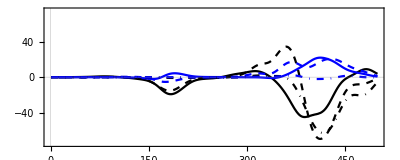

```mathematica
pltnnXXchannelBias=ListLinePlot[Table[channels[theta],{theta,allBiases}],PlotRange->{-75,75},PlotStyle->Values[cols1],AspectRatio->0.4]
```

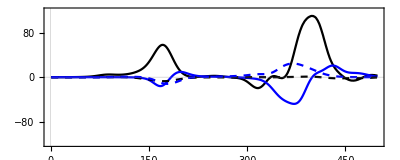

```mathematica
pltnnXXchannelWeights=ListLinePlot[Table[channels[theta],{theta,allWeights}],PlotRange->{-120,120},PlotStyle->Values[cols2],AspectRatio->0.4]
```

```mathematica
SetDirectory[NotebookDirectory[]];
If[!DirectoryQ[figureDir],CreateDirectory[figureDir]];
Export[figureDir<>"/channels_nnXX_bias.pdf",pltnnXXchannelBias]
```

figures_dbm/channels_nnXX_bias.pdf

```mathematica
SetDirectory[NotebookDirectory[]];
If[!DirectoryQ[figureDir],CreateDirectory[figureDir]];
Export[figureDir<>"/channels_nnXX_weights.pdf",pltnnXXchannelWeights]
```

figures_dbm/channels_nnXX_weights.pdf

## True derivative

```mathematica
derivTrue={};
Do[
dataNext=Import["../../stoch_sims/moments_other/"<>IntegerString[timepoint+1,10,4]<>".txt","Table"][[1,3]];
dataThis=Import["../../stoch_sims/moments_other/"<>IntegerString[timepoint,10,4]<>".txt","Table"][[1,3]];
AppendTo[derivTrue,(dataNext-dataThis)/dt];
,{timepoint,0,timepointMax-2}];
```

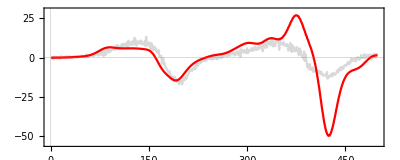

```mathematica
pltSumnnXX=ListLinePlot[{derivTrue,Total[Values[channels]]},PlotStyle->{LightGray,Red},PlotRange->{-55,30},AspectRatio->0.4]
```

```mathematica
SetDirectory[NotebookDirectory[]];
If[!DirectoryQ[figureDir],CreateDirectory[figureDir]];
Export[figureDir<>"/sum_nnXX.pdf",pltSumnnXX]
```

figures_dbm/sum_nnXX.pdf

# Moments: NNNs XY

## Plot

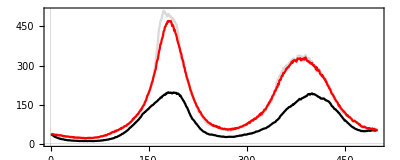

```mathematica
pltnnnXY=Module[{moments,dat,momentsTrue,momentsLP,vs},
vs={"nnn XY"};
moments=Association[];
Do[
moments[v]={};
,{v,vs}];
Do[
dat=Import["../data/"<>dirIxns<>"/"<>dir<>"/"<>IntegerString[timepoint,10,4]<>"/moments/moments_other.txt","Table"];
AppendTo[moments[vs[[1]]],dat[[6,3]]];
,{timepoint,0,timepointMax-1}];

momentsLP=Association[];
Do[
momentsLP[v]={};
,{v,vs}];
Do[
dat=Import["../data/"<>dirIxns<>"/"<>dirLP<>"/"<>IntegerString[timepoint,10,4]<>"/moments/moments_other.txt","Table"];
AppendTo[momentsLP[vs[[1]]],dat[[6,3]]];
,{timepoint,0,timepointMax-1}];

momentsTrue=Association[];
Do[
momentsTrue[v]={};
,{v,vs}];
Do[
dat=Import["../../stoch_sims/moments_other/"<>IntegerString[timepoint,10,4]<>".txt","Table"];
AppendTo[momentsTrue[vs[[1]]],dat[[6,3]]];
,{timepoint,0,timepointMax-1}];

ListLinePlot[{moments[vs[[1]]],momentsTrue[vs[[1]]],momentsLP[vs[[1]]]},PlotStyle->{LightGray,Black,Red},AspectRatio->0.4]
]
```

```mathematica
SetDirectory[NotebookDirectory[]];
If[!DirectoryQ[figureDir],CreateDirectory[figureDir]];
Export[figureDir<>"/moment_nnn_XY.pdf",pltnnnXY]
```

figures_dbm/moment_nnn_XY.pdf

## Channels

```mathematica
{dataCovLP,derivs,channels}=Module[{dataParams,dataCov,tmp,channels,derivs,dataCovLP},

SetDirectory[NotebookDirectory[]];

(* Import params *)
dataParams=Association[];
Do[
dataParams[theta]=Import["../data/"<>dirIxns<>"/ixn_params_lp/"<>theta<>"_"<>IntegerString[optStepRead,10,5]<>".txt","Table"][[;;,2]];
,{theta,allTheta}];

(* Derivs *)
derivs=Association[];
Do[
derivs[theta]=(RotateLeft[dataParams[theta]][[;;-2]]-dataParams[theta][[;;-2]])/dt;
,{theta,allTheta}];

(* Import covs *)
dataCov=Association[];
Do[
dataCov[theta]={};
,{theta,allTheta}];
Do[
tmp=Import["../data/"<>dirIxns<>"/"<>dirLP<>"/"<>IntegerString[timepoint,10,4]<>"/covs/nnn_XY.txt","Table"];
Do[
AppendTo[dataCov[tmp[[i,1]]],tmp[[i,2]]];
,{i,1,Length[tmp]}];
,{timepoint,0,timepointMax-1}];
dataCovLP=Association[];
Do[
dataCovLP[theta]=LowpassFilter[dataCov[theta],0.1];
,{theta,allTheta}];

(* Multiply *)
channels=Association[];
Do[
channels[theta]={};
,{theta,allTheta}];

Do[
Do[
AppendTo[channels[theta],dataCovLP[theta][[timepoint+1]]*derivs[theta][[timepoint+1]]];
,{theta,allTheta}];

,{timepoint,0,timepointMax-2}];

{dataCovLP,derivs,channels}
];
```

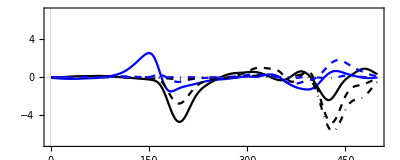

```mathematica
pltnnnXYchannelBias=ListLinePlot[Table[channels[theta],{theta,allBiases}],PlotRange->{-7,7},PlotStyle->Values[cols1],AspectRatio->0.4]
```

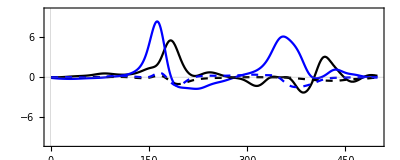

```mathematica
pltnnnXYchannelWeights=ListLinePlot[Table[channels[theta],{theta,allWeights}],PlotRange->{-10,10},PlotStyle->Values[cols2],AspectRatio->0.4]
```

```mathematica
SetDirectory[NotebookDirectory[]];
If[!DirectoryQ[figureDir],CreateDirectory[figureDir]];
Export[figureDir<>"/channels_nnnXY_bias.pdf",pltnnnXYchannelBias]
```

figures_dbm/channels_nnnXY_bias.pdf

```mathematica
SetDirectory[NotebookDirectory[]];
If[!DirectoryQ[figureDir],CreateDirectory[figureDir]];
Export[figureDir<>"/channels_nnnXY_weights.pdf",pltnnnXYchannelWeights]
```

figures_dbm/channels_nnnXY_weights.pdf

## True derivative

```mathematica
derivTrue={};
Do[
dataNext=Import["../../stoch_sims/moments_other/"<>IntegerString[timepoint+1,10,4]<>".txt","Table"][[6,3]];
dataThis=Import["../../stoch_sims/moments_other/"<>IntegerString[timepoint,10,4]<>".txt","Table"][[6,3]];
AppendTo[derivTrue,(dataNext-dataThis)/dt];
,{timepoint,0,timepointMax-2}];
```

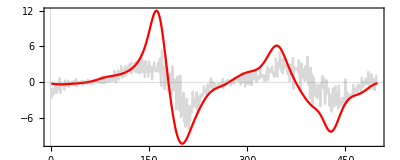

```mathematica
pltSumnnnXY=ListLinePlot[{derivTrue,Total[Values[channels]]},PlotStyle->{LightGray,Red},PlotRange->All,AspectRatio->0.4]
```

```mathematica
SetDirectory[NotebookDirectory[]];
If[!DirectoryQ[figureDir],CreateDirectory[figureDir]];
Export[figureDir<>"/sum_nnnXY.pdf",pltSumnnnXY]
```

figures_dbm/sum_nnnXY.pdf